```mathematica
ωdef[s_,I_,d_,T_]:=s*Exp[(d-I)*T]
```

```mathematica
lhs[s_,f_,T_]:=Exp[f*T]
```

```mathematica
F[ω_,σ_]:=1/2(1+Erf[(-Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
Fc[ω_,σ_]:=1/2(1-Erf[(-Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
rhs1[s_,I_,d_,T_,σ_]:=Exp[d*T]*F[ωdef[s,I,d,T],σ]+Exp[I*T]/s*Fc[ωdef[s,I,d,T],σ]
```

```mathematica
Fe[ω_,σ_]:=1/2(1+Erf[(-Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
Fec[ω_,σ_]:=1/2(1+Erf[(-Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
rhs2[s_,I_,d_,T_,σ_]:=Exp[I*T]/(1-s)*Fe[ωdef[s,I,d,T],σ]-(s*Exp[d*T])/(1-s)*Fec[ωdef[s,I,d,T],σ]
```

```mathematica
sol[I_?NumericQ,fd_?NumericQ,fe_?NumericQ,T_?NumericQ,σ_?NumericQ]:=FindRoot[{lhs[s,fd,T]==rhs1[s,I,d,T,σ],lhs[s,fe,T]==rhs2[s,I,d,T,σ]},{{d,0.015,0.,0.999},{s,0.5,0.001,0.999}},AccuracyGoal->8,PrecisionGoal->8,MaxIterations->1000 (*Guess,Min,Max*)]
```

```mathematica
sol[0.015,0.01,0.05,30,0.3]
```

{d→0.0120893,s→0.930247}

```mathematica
sd[I_?NumericQ,fd_?NumericQ,fe_?NumericQ,T_?NumericQ,σ_?NumericQ]:=s/. sol[I,fd,fe,T,σ]
```

FindRoot::reged: The point {0.0480781,0.999} is at the edge of the search region {0.001,0.999} in coordinate 2 and the computed search direction points outside the region.

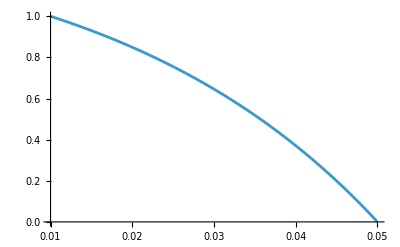

```mathematica
Plot[sd[I,0.01,0.05,30,0.5],{I,0.01,0.05}]
```

```mathematica
rd[I_?NumericQ,fd_?NumericQ,fe_?NumericQ,T_?NumericQ,σ_?NumericQ]:=d/. sol[I,fd,fe,T,σ]
```

```mathematica
WACC[I_?NumericQ,fd_?NumericQ,fe_?NumericQ,T_?NumericQ,σ_?NumericQ]:=Log[sd[I,fd,fe,T,σ]*Exp[rd[I,fd,fe,T,σ]*T]+(1-sd[I,fd,fe,T,σ])*Exp[fe*T]]/T
```

```mathematica
WACC[0.03,0.01,0.05,30,1.0]
```

0.0320415

FindRoot::jsing: Encountered a singular Jacobian at the point {d,s} = {0.015,0.5}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

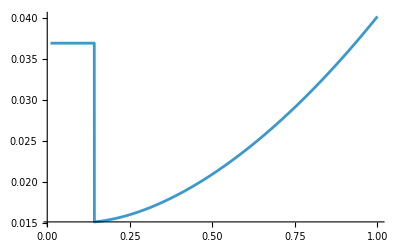

```mathematica
Plot[WACC[0.015,0.01,0.05,30,σ],{σ,0.01,1.0},PlotRange->Full]
```